```mathematica
data=Quiet[Table[{Quantity[10^t,"Years"],UniverseModelData[Quantity[10^t,"Years"],p]},{p,{"DarkEnergyDensityRatio","MatterEnergyDensityRatio","RadiationEnergyDensityRatio"}},{t,3,11,0.2}]];
```

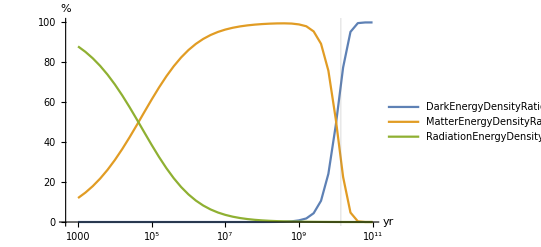

```mathematica
ListLogLinearPlot[data,PlotRange->All,Joined->True,AxesLabel->Automatic,GridLines->{{13.8*10^9},None},PlotLegends->{"DarkEnergyDensityRatio","MatterEnergyDensityRatio","RadiationEnergyDensityRatio"}]
```

```mathematica
data
```

{{{1000. yr,1.39304×10^-12 %},{1584.89 yr,3.46484×10^-12 %},{2511.89 yr,8.60004×10^-12 %},{3981.07 yr,2.12951×10^-11 %},{6309.57 yr,5.25892×10^-11 %},{10000. yr,1.29492×10^-10 %},{15848.9 yr,3.17873×10^-10 %},{25118.9 yr,7.77902×10^-10 %},{39810.7 yr,1.89815×10^-9 %},{63095.7 yr,4.61996×10^-9 %},{100000. yr,1.12231×10^-8 %},{158489. yr,2.72338×10^-8 %},{251189. yr,6.60737×10^-8 %},{398107. yr,1.60434×10^-7 %},{630957. yr,3.90217×10^-7 %},{1.×10^6 yr,9.51443×10^-7 %},{1.58489×10^6 yr,2.32679×10^-6 %},{2.51189×10^6 yr,5.70893×10^-6 %},{3.98107×10^6 yr,0.0000140541 %},{6.30957×10^6 yr,0.0000347095 %},{1.×10^7 yr,0.0000859769 %},{1.58489×10^7 yr,0.000213529 %},{2.51189×10^7 yr,0.000531513 %},{3.98107×10^7 yr,0.00132555 %},{6.30957×10^7 yr,0.00331095 %},{1.×10^8 yr,0.00828033 %},{1.58489×10^8 yr,0.020728 %},{2.51189×10^8 yr,0.0519227 %},{3.98107×10^8 yr,0.130103 %},{6.30957×10^8 yr,0.325898 %},{1.×10^9 yr,0.81504 %},{1.58489×10^9 yr,1.78815 %},{2.51189×10^9 yr,4.41427 %},{3.98107×10^9 yr,10.6334 %},{6.30957×10^9 yr,24.1639 %},{1.×10^10 yr,48.3797 %},{1.58489×10^10 yr,77.4418 %},{2.51189×10^10 yr,95.2808 %},{3.98107×10^10 yr,99.6604 %},{6.30957×10^10 yr,99.995 %},{1.×10^11 yr,100. %}},{{1000. yr,12.015 %},{1584.89 yr,14.7373 %},{2511.89 yr,17.9695 %},{3981.07 yr,21.7563 %},{6309.57 yr,26.1235 %},{10000. yr,31.0675 %},{15848.9 yr,36.5458 %},{25118.9 yr,42.4699 %},{39810.7 yr,48.7046 %},{63095.7 yr,55.0749 %},{100000. yr,61.3825 %},{158489. yr,67.4279 %},{251189. yr,73.0353 %},{398107. yr,78.0723 %},{630957. yr,82.4614 %},{1.×10^6 yr,86.18 %},{1.58489×10^6 yr,89.2519 %},{2.51189×10^6 yr,91.7342 %},{3.98107×10^6 yr,93.7026 %},{6.30957×10^6 yr,95.2391 %},{1.×10^7 yr,96.4229 %},{1.58489×10^7 yr,97.3255 %},{2.51189×10^7 yr,98.0079 %},{3.98107×10^7 yr,98.5201 %},{6.30957×10^7 yr,98.9016 %},{1.×10^8 yr,99.1823 %},{1.58489×10^8 yr,99.3821 %},{2.51189×10^8 yr,99.5084 %},{3.98107×10^8 yr,99.547 %},{6.30957×10^8 yr,99.4381 %},{1.×10^9 yr,99.014 %},{1.58489×10^9 yr,98.0841 %},{2.51189×10^9 yr,95.4978 %},{3.98107×10^9 yr,89.3109 %},{6.30957×10^9 yr,75.8072 %},{1.×10^10 yr,51.612 %},{1.58489×10^10 yr,22.5599 %},{2.51189×10^10 yr,4.72123 %},{3.98107×10^10 yr,0.340087 %},{6.30957×10^10 yr,0.00506407 %},{1.×10^11 yr,6.41915×10^-6 %}},{{1000. yr,87.985 %},{1584.89 yr,85.2627 %},{2511.89 yr,82.0305 %},{3981.07 yr,78.2437 %},{6309.57 yr,73.8765 %},{10000. yr,68.9325 %},{15848.9 yr,63.4542 %},{25118.9 yr,57.5301 %},{39810.7 yr,51.2955 %},{63095.7 yr,44.9251 %},{100000. yr,38.6175 %},{158489. yr,32.5721 %},{251189. yr,26.9648 %},{398107. yr,21.9277 %},{630957. yr,17.5386 %},{1.×10^6 yr,13.8201 %},{1.58489×10^6 yr,10.7482 %},{2.51189×10^6 yr,8.26583 %},{3.98107×10^6 yr,6.29744 %},{6.30957×10^6 yr,4.76102 %},{1.×10^7 yr,3.57719 %},{1.58489×10^7 yr,2.67452 %},{2.51189×10^7 yr,1.99192 %},{3.98107×10^7 yr,1.4791 %},{6.30957×10^7 yr,1.09576 %},{1.×10^8 yr,0.810324 %},{1.58489×10^8 yr,0.598394 %},{2.51189×10^8 yr,0.441357 %},{3.98107×10^8 yr,0.325116 %},{6.30957×10^8 yr,0.239041 %},{1.×10^9 yr,0.175105 %},{1.58489×10^9 yr,0.133074 %},{2.51189×10^9 yr,0.095017 %},{3.98107×10^9 yr,0.0648253 %},{6.30957×10^9 yr,0.0396267 %},{1.×10^10 yr,0.0188311 %},{1.58489×10^10 yr,0.00534017 %},{2.51189×10^10 yr,0.000619206 %},{3.98107×10^10 yr,0.0000182827 %},{6.30957×10^10 yr,6.69016×10^-8 %},{1.×10^11 yr,9.17768×10^-12 %}}}